# Woods-Saxon Potential

## Micah Buuck

6/17/13

## Constants and Initial Conditions

Originally I tried to make use of Mathematica's built-in unit handling, but I couldn't figure out how to make that work with plotting, so I gave up. I left the code for it in, but commented it out.

```mathematica
(*<<Units`
Needs["PhysicalConstants`"]*)
Needs["PlotLegends`"]
```

```mathematica
m=938.272046(*Mega ElectronVolt*);
ℏc=197.32697178(*Mega ElectronVolt*Femto Meter*);
R=3 (*Femto Meter*);
V0=(-1.9-.38*I)*ℏc^2/(2*m) (*Mega ElectronVolt*);
a=.54 (*Femto Meter*);
V[r_]:=V0/(1+E^((r-R)/a));
```

### Plot for potential

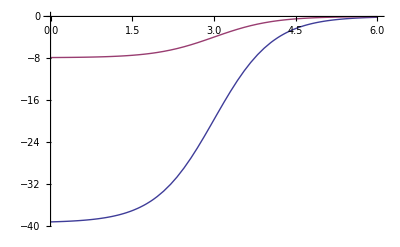

```mathematica
Plot[{Re[V[r]],Im[V[r]]},{r,0,2*R}]
```

## Solve the Schrödinger Equation

First I solve the Schrödinger equation for the radial wavefunction with an arbitrary constant for the initial condition for u'(0). My goal is to show that the resulting phase shift we get from this in independent of the choice of u'(0).

```mathematica
s[L_,k_,b_]:=NDSolve[{u''[r]+(k^2-2*m/(ℏc)^2*V[r]-L*(L+1)/r^2)*u[r]==0,u[(1000*k)^(-1)]==0,u'[(1000*k)^(-1)]==b},u,{r,(1000*k)^(-1),5*R}]
```

```mathematica
u[L_,k_,r_,b_]:=u[r]/.s[L,k,b][[1]]
```

```mathematica
β[L_,k_,b_]:=5*R/Evaluate[u[L,k,5*R,b]]*(D[u[L,k,r,b],r]/.r->(5*R))-1
tanδ[L_,k_,b_]:=N[(k*5*R*Derivative[0,1][SphericalBesselJ][L,k*5*R]-β[L,k,b]*SphericalBesselJ[L,k*5*R])/(k*5*R*Derivative[0,1][SphericalBesselY][L,k*5*R]-β[L,k,b]*SphericalBesselY[L,k*5*R])]
```

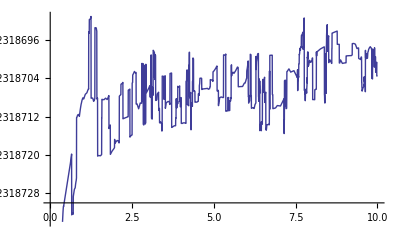

```mathematica
Plot[Re[tanδ[0,1,b]],{b,0.01,10}]
```

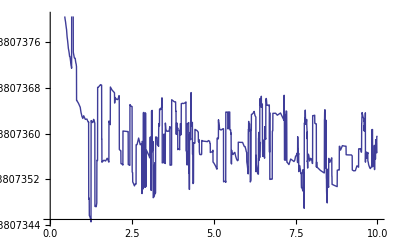

```mathematica
Plot[Im[tanδ[0,1,b]],{b,0.01,10}]
```

As we can see from this plot of tanδ vs. u'(0), the phase shift appears to be independent of our choice of u'(0) up to about 0.01% error.

## Reformulate tanδ for specific choice of u'(0)

These are the same equations as above, but now we have chosen u'(0)=8 (an arbitrary choice).

```mathematica
s[L_,k_]:=NDSolve[{u''[r]+(k^2-2*m/(ℏc)^2*V[r]-L*(L+1)/r^2)*u[r]==0,u[(1000*k)^(-1)]==0,u'[(1000*k)^(-1)]==8},u,{r,(1000*k)^(-1),5*R},MaxSteps->20000]
```

```mathematica
u[L_,k_,r_]:=u[r]/.s[L,k][[1]]
```

```mathematica
β[L_,k_]:=5*R/Evaluate[u[L,k,5*R]]*(D[u[L,k,r],r]/.r->(5*R))-1
tanδ[L_,k_]:=N[(k*5*R*Derivative[0,1][SphericalBesselJ][L,k*5*R]-β[L,k]*SphericalBesselJ[L,k*5*R])/(k*5*R*Derivative[0,1][SphericalBesselY][L,k*5*R]-β[L,k]*SphericalBesselY[L,k*5*R])]
```

```mathematica
Table[tanδ[L,1],{L,0,20}]
```

{-0.923187+0.738074 ⅈ,-1.22237+1.20904 ⅈ,-1.58735+1.99802 ⅈ,1.00564+1.1644 ⅈ,0.211335+0.0713622 ⅈ,0.0403135+0.00963108 ⅈ,0.00812726+0.00172725 ⅈ,0.00165119+0.000337094 ⅈ,0.000333925+0.0000672485 ⅈ,0.0000671337+0.0000134576 ⅈ,0.0000134081+2.6876×10^-6 ⅈ,2.6722×10^-6+5.35051×10^-7 ⅈ,5.30794×10^-7+1.06139×10^-7 ⅈ,1.05238×10^-7+2.09407×10^-8 ⅈ,2.36222×10^-8+4.08615×10^-9 ⅈ,6.62046×10^-9+7.80279×10^-10 ⅈ,1.01519×10^-9+1.43713×10^-10 ⅈ,1.04656×10^-10+2.51393×10^-11 ⅈ,-3.4111×10^-12+4.1209×10^-12 ⅈ,-3.93433×10^-12+6.26806×10^-13 ⅈ,-1.06641×10^-13+8.79197×10^-14 ⅈ}

For k=1, tanδ becomes negligible after about L=5. This is also evident in the plot for continuous L below.

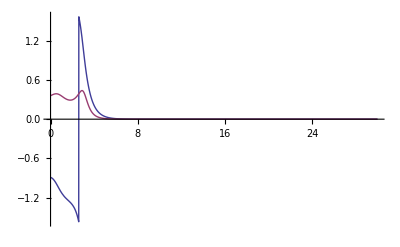

```mathematica
Plot[{Re[ArcTan[tanδ[L,1]]],Im[ArcTan[tanδ[L,1]]]},{L,0,30},PlotRange->{-Pi/2,Pi/2}]
```

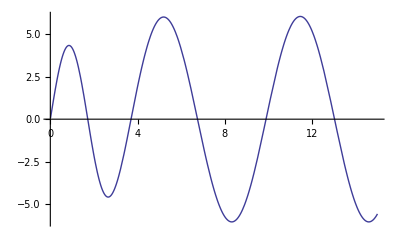

```mathematica
Plot[Evaluate[u[0,1,r]],{r,(100)^(-1),5*R}]
```

Plugging this phase shift into the equations for the scattering amplitude is:

```mathematica
f[k_,θ_]:=1/k*Sum[(2*L+1)*tanδ[L,k]/(1-I*tanδ[L,k])*LegendreP[L,Cos[θ]],{L,0,2*k*R}]
```

Here is a table of some values of dσ/dΩ as a function of θ.

```mathematica
Clear[dσdΩ]
```

```mathematica
dσdΩ[k_,points_:10]:=Table[{θ,Abs[f[k,θ]]^2},{θ,0,Pi,N[1/points]}]
```

```mathematica
dσdΩ[1]
```

```mathematica
{{0.,138.24735648211183},{0.1,131.96418694419444},{0.2,114.6592654903783},{0.30000000000000004,90.39468602293465},{0.4,64.30834749550795},{0.5,40.96502717809941},{0.6000000000000001,23.185107373198356},{0.7000000000000001,11.715122859819573},{0.8,5.663523548401128},{0.9,3.3198513944892047},{1.,2.9319238824176685},{1.1,3.1817325211565817},{1.2000000000000002,3.323652386316457},{1.3,3.0953167489705633},{1.4000000000000001,2.5414915172058445},{1.5,1.8454757211071333},{1.6,1.2047526866685199},{1.7000000000000002,0.7547245075757844},{1.8,0.53626863531564},{1.9000000000000001,0.5023777111949094},{2.,0.5545725801561825},{2.1,0.5922118641706786},{2.2,0.5545270708340819},{2.3000000000000003,0.44029499749236833},{2.4000000000000004,0.3009951398837256},{2.5,0.21397933778536093},{2.6,0.2479553016653255},{2.7,0.43331787347604256},{2.8000000000000003,0.7467074651808787},{2.9000000000000004,1.1146726795353727},{3.,1.4359192277790755},{3.1,1.6154058368157207}}
```

{{0.,138.247},{0.1,131.964},{0.2,114.659},{0.3,90.3947},{0.4,64.3083},{0.5,40.965},{0.6,23.1851},{0.7,11.7151},{0.8,5.66352},{0.9,3.31985},{1.,2.93192},{1.1,3.18173},{1.2,3.32365},{1.3,3.09532},{1.4,2.54149},{1.5,1.84548},{1.6,1.20475},{1.7,0.754725},{1.8,0.536269},{1.9,0.502378},{2.,0.554573},{2.1,0.592212},{2.2,0.554527},{2.3,0.440295},{2.4,0.300995},{2.5,0.213979},{2.6,0.247955},{2.7,0.433318},{2.8,0.746707},{2.9,1.11467},{3.,1.43592},{3.1,1.61541}}

```mathematica
interp1=Interpolation[%]
```

InterpolatingFunction[{{0.,3.1}},<>]

Here is a log plot of that same information.

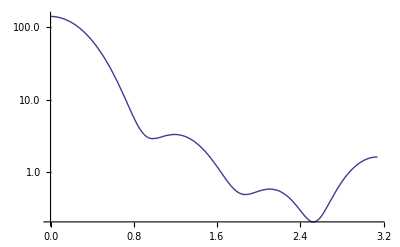

```mathematica
p1=LogPlot[interp1[θ],{θ,0,Pi}]
```

## Eikonal Approximation

These equations come straight out of Sakurai, equations 7.4.13 and 7.4.14 (page 394).

```mathematica
χ0[k_,b_]=-2*m/(k*(ℏc)^2)*NIntegrate[V[Sqrt[b^2+z^2]],{z,0,15}];
T0[k_,b_]:=Exp[I*χ0[k,b]]-1
Eif0[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T0[k,b],{b,0,15}]
```

I had to have the iteration of the table below happen in integer steps because doing it in decimal steps was giving Mathematica problems somehow. I think it probably has something to do with differences in the way it handles integers and floats.

```mathematica
eik0dσdΩ[k_,points_:10]:=Table[{N[θ/points],Abs[Eif0[k,θ/points]]^2},{θ,0,points*Pi,1}]
```

```mathematica
eik0dσdΩ[1]
```

```mathematica
{{0,77.81449298353003},{0.1,74.35383330732927},{0.2,64.84837991679096},{0.30000000000000004,51.57988020244924},{0.4,37.37770256118771},{0.5,24.684171090312795},{0.6000000000000001,14.948965384363145},{0.7000000000000001,8.51791645462917},{0.8,4.915230121696361},{0.9,3.281874841998521},{1.,2.7553515339408743},{1.1,2.6857105335099236},{1.2000000000000002,2.6902902457515094},{1.3,2.6068136696049393},{1.4000000000000001,2.4104679946468877},{1.5,2.1388434537513845},{1.6,1.8425250325094127},{1.7000000000000002,1.5611567627514344},{1.8,1.3170427344045403},{1.9000000000000001,1.1176866720757859},{2.,0.9611434858445198},{2.1,0.8409452369136389},{2.2,0.7494715126304502},{2.3000000000000003,0.6797742195028705},{2.4000000000000004,0.6262920150255549},{2.5,0.5849232679639141},{2.6,0.5528078924322809},{2.7,0.5280292166366286},{2.8000000000000003,0.5093396281148677},{2.9000000000000004,0.4959471492852086},{3.,0.48736597027500483},{3.1,0.48332051398465925}}
```

{{0,77.8145},{0.1,74.3538},{0.2,64.8484},{0.3,51.5799},{0.4,37.3777},{0.5,24.6842},{0.6,14.949},{0.7,8.51792},{0.8,4.91523},{0.9,3.28187},{1.,2.75535},{1.1,2.68571},{1.2,2.69029},{1.3,2.60681},{1.4,2.41047},{1.5,2.13884},{1.6,1.84253},{1.7,1.56116},{1.8,1.31704},{1.9,1.11769},{2.,0.961143},{2.1,0.840945},{2.2,0.749472},{2.3,0.679774},{2.4,0.626292},{2.5,0.584923},{2.6,0.552808},{2.7,0.528029},{2.8,0.50934},{2.9,0.495947},{3.,0.487366},{3.1,0.483321}}

```mathematica
eik0interp1=Interpolation[%]
```

InterpolatingFunction[{{0.,3.1}},<>]

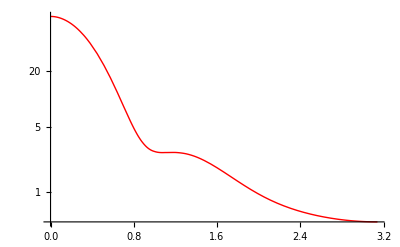

```mathematica
eik0p1=LogPlot[eik0interp1[θ],{θ,0,Pi},PlotStyle->Red]
```

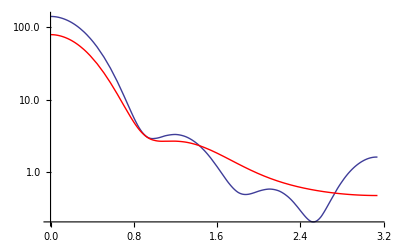

```mathematica
Show[p1,eik0p1]
```

As you can see above, the two plots actually agree with each other pretty well, especially at small θ. There is some pretty obvious disagreement for large θ, however, and the eikonal approximation seems to miss some of the structure apparent in the partial wave formulation.

## Check Method for k=10

For k=10, then k^2 = 100 >> 2*m*V/ℏ^2 ~= -2 - 0.4i, so the eikonal approximation should be valid.

```mathematica
dσdΩ[10]//Timing
```

{510.822,{{0.,486.366},{0.1,13.7655},{0.2,0.142722},{0.3,0.00212583},{0.4,0.000122783},{0.5,1.06992×10^-6},{0.6,3.82125×10^-6},{0.7,1.5606×10^-6},{0.8,9.09828×10^-7},{0.9,4.56746×10^-7},{1.,2.06863×10^-7},{1.1,7.29154×10^-8},{1.2,1.35146×10^-8},{1.3,1.44845×10^-9},{1.4,1.86539×10^-8},{1.5,5.22517×10^-8},{1.6,9.36151×10^-8},{1.7,1.35377×10^-7},{1.8,1.73879×10^-7},{1.9,2.03822×10^-7},{2.,2.24481×10^-7},{2.1,2.3388×10^-7},{2.2,2.31779×10^-7},{2.3,2.17965×10^-7},{2.4,1.94183×10^-7},{2.5,1.61737×10^-7},{2.6,1.23014×10^-7},{2.7,8.11484×10^-8},{2.8,4.02909×10^-8},{2.9,8.73381×10^-9},{3.,6.19344×10^-9},{3.1,1.49821×10^-7}}}

The first number above is the time that command took to evaluate.

```mathematica
interp10=Interpolation[%[[2]]];
```

InterpolatingFunction[{{0.,3.1}},<>]

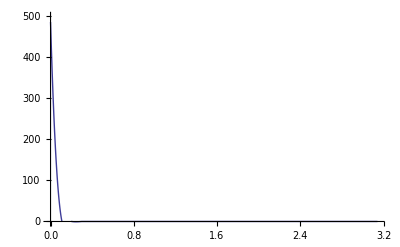

```mathematica
p10=Plot[interp10[θ],{θ,0,Pi},PlotRange->{-1,500}]
```

```mathematica
eik0dσdΩ[10]//Timing
```

{225.703,{{0,486.162},{0.1,14.0605},{0.2,0.13689},{0.3,0.00246745},{0.4,0.0000540022},{0.5,1.42675×10^-6},{0.6,3.23853×10^-8},{0.7,1.29725×10^-9},{0.8,5.91253×10^-11},{0.9,1.26869×10^-11},{1.,8.34575×10^-12},{1.1,3.54278×10^-12},{1.2,2.08122×10^-12},{1.3,1.19259×10^-12},{1.4,7.31612×10^-13},{1.5,4.70504×10^-13},{1.6,3.14678×10^-13},{1.7,2.18652×10^-13},{1.8,1.57428×10^-13},{1.9,1.16839×10^-13},{2.,8.94036×10^-14},{2.1,7.03232×10^-14},{2.2,5.67563×10^-14},{2.3,4.69704×10^-14},{2.4,3.98201×10^-14},{2.5,3.45317×10^-14},{2.6,3.05815×10^-14},{2.7,2.77058×10^-14},{2.8,2.55993×10^-14},{2.9,2.41731×10^-14},{3.,2.32565×10^-14},{3.1,2.28285×10^-14}}}

You can see that as k increases, the eikonal approximation evaluates faster than the partial wave expansion, as we would expect.

```mathematica
eik0interp10=Interpolation[%[[2]]];
```

InterpolatingFunction[{{0.,3.1}},<>]

The points we evaluated dσ/dΩ at are not dense enough to really capture all the detail at small θ, so that's why the plots for k = 10 aren't very good. A better interpolation could be made, but it would take some time.

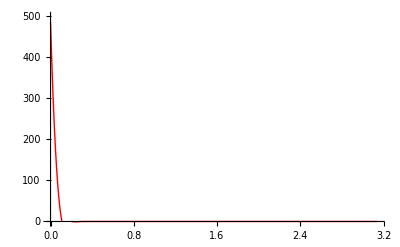

```mathematica
eik0p10=Plot[eik0interp10[θ],{θ,0,Pi},PlotRange->{-1,500},PlotStyle->Red]
```

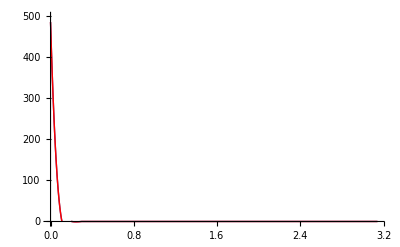

```mathematica
Show[p10,eik0p10]
```

## Plots for k=1,2,3

```mathematica
dσdΩ[2]
```

{{0.,294.133},{0.1,254.454},{0.2,163.583},{0.3,76.4455},{0.4,25.1958},{0.5,6.35473},{0.6,2.53503},{0.7,2.01532},{0.8,1.36054},{0.9,0.647556},{1.,0.246628},{1.1,0.124859},{1.2,0.0972809},{1.3,0.0693531},{1.4,0.0399179},{1.5,0.0199396},{1.6,0.00965119},{1.7,0.00640806},{1.8,0.00574316},{1.9,0.00435876},{2.,0.00275605},{2.1,0.00182001},{2.2,0.00102615},{2.3,0.000486702},{2.4,0.000452967},{2.5,0.000407829},{2.6,0.000224844},{2.7,0.000165988},{2.8,0.000223775},{2.9,0.000166481},{3.,0.000245865},{3.1,0.000613277}}

```mathematica
interp2=Interpolation[%];
```

```mathematica
eik0dσdΩ[2]
```

NIntegrate::inumr: The integrand -39.42463943157022`  + 7.884927886314045` ⅈ/1 + ⅇ^1.8518518518518516` (-3 + √Plus[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{{0,251.192},{0.1,218.078},{0.2,142.436},{0.3,69.6934},{0.4,25.7959},{0.5,8.17661},{0.6,3.44878},{0.7,2.25907},{0.8,1.46341},{0.9,0.785982},{1.,0.37341},{1.1,0.186334},{1.2,0.110689},{1.3,0.0727448},{1.4,0.0468667},{1.5,0.028506},{1.6,0.0168265},{1.7,0.0101767},{1.8,0.00658463},{1.9,0.00457904},{2.,0.0033391},{2.1,0.00248921},{2.2,0.00187436},{2.3,0.00142542},{2.4,0.00110132},{2.5,0.000870884},{2.6,0.000709192},{2.7,0.000597083},{2.8,0.00052068},{2.9,0.000470474},{3.,0.000440333},{3.1,0.000426674}}

```mathematica
eik0interp2=Interpolation[%];
```

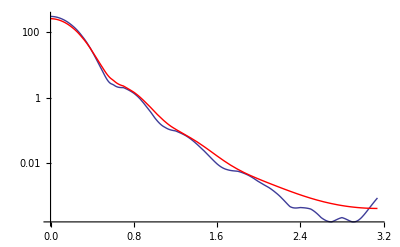

```mathematica
p2=LogPlot[interp2[θ],{θ,0,Pi}];
eik0p2=LogPlot[eik0interp2[θ],{θ,0,Pi},PlotStyle->Red];
Show[p2,eik0p2]
```

```mathematica
dσdΩ[3,100]
```

{{0.,372.486},{0.01,371.356},{0.02,367.986},{0.03,362.434},{0.04,354.793},{0.05,345.194},{0.06,333.795},{0.07,320.782},{0.08,306.364},{0.09,290.763},{0.1,274.217},{0.11,256.964},{0.12,239.246},{0.13,221.298},{0.14,203.343},{0.15,185.591},{0.16,168.235},{0.17,151.444},{0.18,135.366},{0.19,120.122},{0.2,105.81},{0.21,92.5011},{0.22,80.2424},{0.23,69.0582},{0.24,58.9514},{0.25,49.9061},{0.26,41.8898},{0.27,34.8563},{0.28,28.7482},{0.29,23.5},{0.3,19.0402},{0.31,15.2942},{0.32,12.1859},{0.33,9.64032},{0.34,7.58442},{0.35,5.94904},{0.36,4.66956},{0.37,3.68674},{0.38,2.94714},{0.39,2.40331},{0.4,2.01384},{0.41,1.74319},{0.42,1.56136},{0.43,1.44355},{0.44,1.36963},{0.45,1.32368},{0.46,1.29345},{0.47,1.26984},{0.48,1.24638},{0.49,1.21879},{0.5,1.18455},{0.51,1.14249},{0.52,1.09247},{0.53,1.0351},{0.54,0.97149},{0.55,0.903061},{0.56,0.831379},{0.57,0.758034},{0.58,0.684554},{0.59,0.612336},{0.6,0.5426},{0.61,0.476366},{0.62,0.414443},{0.63,0.357426},{0.64,0.305709},{0.65,0.259494},{0.66,0.218815},{0.67,0.18356},{0.68,0.153491},{0.69,0.128275},{0.7,0.107501},{0.71,0.0907107},{0.72,0.0774132},{0.73,0.0671094},{0.74,0.0593072},{0.75,0.0535364},{0.76,0.0493604},{0.77,0.0463852},{0.78,0.0442654},{0.79,0.0427075},{0.8,0.0414711},{0.81,0.0403676},{0.82,0.0392572},{0.83,0.0380441},{0.84,0.0366712},{0.85,0.035114},{0.86,0.0333735},{0.87,0.0314702},{0.88,0.0294379},{0.89,0.0273182},{0.9,0.0251555},{0.91,0.0229936},{0.92,0.0208726},{0.93,0.0188267},{0.94,0.0168835},{0.95,0.0150631},{0.96,0.0133786},{0.97,0.0118366},{0.98,0.0104383},{0.99,0.00918038},{1.,0.00805638},{1.01,0.00705766},{1.02,0.00617445},{1.03,0.00539665},{1.04,0.00471438},{1.05,0.00411843},{1.06,0.00360048},{1.07,0.00315312},{1.08,0.00276985},{1.09,0.00244488},{1.1,0.00217301},{1.11,0.00194937},{1.12,0.00176928},{1.13,0.00162808},{1.14,0.00152105},{1.15,0.00144331},{1.16,0.00138987},{1.17,0.00135567},{1.18,0.00133563},{1.19,0.00132482},{1.2,0.00131856},{1.21,0.00131261},{1.22,0.00130323},{1.23,0.0012874},{1.24,0.00126281},{1.25,0.00122802},{1.26,0.00118239},{1.27,0.00112613},{1.28,0.00106019},{1.29,0.000986144},{1.3,0.0009061},{1.31,0.000822483},{1.32,0.00073788},{1.33,0.000654851},{1.34,0.000575755},{1.35,0.000502607},{1.36,0.000436954},{1.37,0.000379806},{1.38,0.000331604},{1.39,0.000292235},{1.4,0.000261088},{1.41,0.00023715},{1.42,0.000219124},{1.43,0.000205557},{1.44,0.000194977},{1.45,0.000186013},{1.46,0.000177496},{1.47,0.00016853},{1.48,0.000158536},{1.49,0.000147251},{1.5,0.000134707},{1.51,0.000121178},{1.52,0.000107114},{1.53,0.0000930599},{1.54,0.0000795797},{1.55,0.0000671894},{1.56,0.0000563015},{1.57,0.0000471905},{1.58,0.000039978},{1.59,0.0000346375},{1.6,0.0000310148},{1.61,0.0000288599},{1.62,0.0000278651},{1.63,0.0000277027},{1.64,0.000028059},{1.65,0.0000286597},{1.66,0.0000292856},{1.67,0.0000297779},{1.68,0.0000300347},{1.69,0.0000300005},{1.7,0.0000296531},{1.71,0.000028989},{1.72,0.0000280128},{1.73,0.0000267298},{1.74,0.0000251444},{1.75,0.0000232643},{1.76,0.0000211065},{1.77,0.0000187069},{1.78,0.0000161278},{1.79,0.0000134621},{1.8,0.000010833},{1.81,8.38772×10^-6},{1.82,6.28492×10^-6},{1.83,4.67816×10^-6},{1.84,3.69663×10^-6},{1.85,3.42626×10^-6},{1.86,3.8942×10^-6},{1.87,5.05904×10^-6},{1.88,6.80911×10^-6},{1.89,8.96941×10^-6},{1.9,0.0000113171},{1.91,0.0000136039},{1.92,0.0000155831},{1.93,0.000017037},{1.94,0.000017803},{1.95,0.0000177925},{1.96,0.000017002},{1.97,0.0000155142},{1.98,0.0000134878},{1.99,0.0000111387},{2.,8.71355×10^-6},{2.01,6.46029×10^-6},{2.02,4.59796×10^-6},{2.03,3.29086×10^-6},{2.04,2.62984×10^-6},{2.05,2.62319×10^-6},{2.06,3.19808×10^-6},{2.07,4.21251×10^-6},{2.08,5.47581×10^-6},{2.09,6.77497×10^-6},{2.1,7.9032×10^-6},{2.11,8.68689×10^-6},{2.12,9.00738×10^-6},{2.13,8.81476×10^-6},{2.14,8.13186×10^-6},{2.15,7.04838×10^-6},{2.16,5.70587×10^-6},{2.17,4.27608×10^-6},{2.18,2.93571×10^-6},{2.19,1.8412×10^-6},{2.2,1.10716×10^-6},{2.21,7.91335×10^-7},{2.22,8.88212×10^-7},{2.23,1.33197×10^-6},{2.24,2.00822×10^-6},{2.25,2.7727×10^-6},{2.26,3.47408×10^-6},{2.27,3.97752×10^-6},{2.28,4.18543×10^-6},{2.29,4.05249×10^-6},{2.3,3.59257×10^-6},{2.31,2.87667×10^-6},{2.32,2.02205×10^-6},{2.33,1.17423×10^-6},{2.34,4.84426×10^-7},{2.35,8.58523×10^-8},{2.36,7.2288×10^-8},{2.37,4.82255×10^-7},{2.38,1.29119×10^-6},{2.39,2.41294×10^-6},{2.4,3.71053×10^-6},{2.41,5.01479×10^-6},{2.42,6.14833×10^-6},{2.43,6.95135×10^-6},{2.44,7.3057×10^-6},{2.45,7.15352×10^-6},{2.46,6.50763×10^-6},{2.47,5.45204×10^-6},{2.48,4.13214×10^-6},{2.49,2.73576×10^-6},{2.5,1.46767×10^-6},{2.51,5.2081×10^-7},{2.52,4.84785×10^-8},{2.53,1.41345×10^-7},{2.54,8.12755×10^-7},{2.55,1.9946×10^-6},{2.56,3.54464×10^-6},{2.57,5.26456×10^-6},{2.58,6.92639×10^-6},{2.59,8.30396×10^-6},{2.6,9.20486×10^-6},{2.61,9.49857×10^-6},{2.62,9.13662×10^-6},{2.63,8.16167×10^-6},{2.64,6.70399×10^-6},{2.65,4.96552×10^-6},{2.66,3.19329×10^-6},{2.67,1.64566×10^-6},{2.68,5.56093×10^-7},{2.69,9.92531×10^-8},{2.7,3.64465×10^-7},{2.71,1.34042×10^-6},{2.72,2.9137×10^-6},{2.73,4.88171×10^-6},{2.74,6.97878×10^-6},{2.75,8.91217×10^-6},{2.76,0.0000104033},{2.77,0.0000112283},{2.78,0.0000112531},{2.79,0.0000104563},{2.8,8.93753×10^-6},{2.81,6.90908×10^-6},{2.82,4.67078×10^-6},{2.83,2.57146×10^-6},{2.84,9.61392×10^-7},{2.85,1.42076×10^-7},{2.86,3.2012×10^-7},{2.87,1.57188×10^-6},{2.88,3.82432×10^-6},{2.89,6.85568×10^-6},{2.9,0.000010317},{2.91,0.0000137728},{2.92,0.0000167567},{2.93,0.0000188359},{2.94,0.0000196749},{2.95,0.0000190928},{2.96,0.0000171037},{2.97,0.0000139355},{2.98,0.0000100221},{2.99,5.97019×10^-6},{3.,2.50062×10^-6},{3.01,3.72096×10^-7},{3.02,2.94224×10^-7},{3.03,2.84001×10^-6},{3.04,8.36812×10^-6},{3.05,0.0000169643},{3.06,0.0000284098},{3.07,0.0000421814},{3.08,0.0000574846},{3.09,0.0000733172},{3.1,0.0000885575},{3.11,0.000102068},{3.12,0.000112805},{3.13,0.000119917},{3.14,0.000122835}}

```mathematica
temp=Interpolation[%]
```

InterpolatingFunction[{{0.,3.14}},<>]

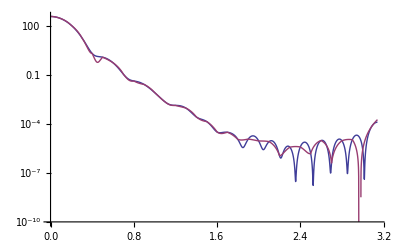

```mathematica
LogPlot[{temp[θ],interp3[θ]},{θ,0,Pi}]
```

```mathematica
interp3=Interpolation[%];
```

```mathematica
eik0dσdΩ[3,100]
```

NIntegrate::inumr: The integrand -39.42463943157022`  + 7.884927886314045` ⅈ/1 + ⅇ^1.8518518518518516` (-3 + √Plus[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{{0.,349.768},{0.01,348.715},{0.02,345.573},{0.03,340.397},{0.04,333.277},{0.05,324.335},{0.06,313.724},{0.07,301.617},{0.08,288.212},{0.09,273.718},{0.1,258.357},{0.11,242.351},{0.12,225.924},{0.13,209.293},{0.14,192.663},{0.15,176.226},{0.16,160.157},{0.17,144.608},{0.18,129.712},{0.19,115.577},{0.2,102.291},{0.21,89.9143},{0.22,78.4895},{0.23,68.0369},{0.24,58.5585},{0.25,50.0395},{0.26,42.4512},{0.27,35.7527},{0.28,29.8938},{0.29,24.8171},{0.3,20.4603},{0.31,16.7582},{0.32,13.6446},{0.33,11.0536},{0.34,8.92142},{0.35,7.18716},{0.36,5.79369},{0.37,4.68831},{0.38,3.82313},{0.39,3.15526},{0.4,2.64687},{0.41,2.26509},{0.42,1.98177},{0.43,1.77325},{0.44,1.61995},{0.45,1.50598},{0.46,1.41875},{0.47,1.34851},{0.48,1.28799},{0.49,1.23194},{0.5,1.17683},{0.51,1.12044},{0.52,1.06165},{0.53,1.0001},{0.54,0.93601},{0.55,0.869987},{0.56,0.802864},{0.57,0.735581},{0.58,0.669096},{0.59,0.604314},{0.6,0.54204},{0.61,0.48295},{0.62,0.427573},{0.63,0.376294},{0.64,0.329351},{0.65,0.286851},{0.66,0.248785},{0.67,0.215042},{0.68,0.185433},{0.69,0.159703},{0.7,0.137557},{0.71,0.118667},{0.72,0.102693},{0.73,0.0892927},{0.74,0.0781301},{0.75,0.0688864},{0.76,0.0612639},{0.77,0.0549907},{0.78,0.0498229},{0.79,0.045546},{0.8,0.0419746},{0.81,0.0389514},{0.82,0.036346},{0.83,0.0340521},{0.84,0.0319856},{0.85,0.0300815},{0.86,0.0282915},{0.87,0.0265815},{0.88,0.0249286},{0.89,0.0233193},{0.9,0.0217471},{0.91,0.0202109},{0.92,0.0187132},{0.93,0.0172588},{0.94,0.015854},{0.95,0.0145052},{0.96,0.0132189},{0.97,0.0120006},{0.98,0.0108549},{0.99,0.00978523},{1.,0.00879354},{1.01,0.00788061},{1.02,0.00704594},{1.03,0.00628792},{1.04,0.00560397},{1.05,0.00499067},{1.06,0.00444399},{1.07,0.0039594},{1.08,0.00353206},{1.09,0.00315698},{1.1,0.0028291},{1.11,0.00254344},{1.12,0.00229521},{1.13,0.00207983},{1.14,0.00189302},{1.15,0.00173083},{1.16,0.00158969},{1.17,0.00146637},{1.18,0.00135803},{1.19,0.00126217},{1.2,0.00117665},{1.21,0.00109965},{1.22,0.00102962},{1.23,0.000965322},{1.24,0.000905718},{1.25,0.000849997},{1.26,0.000797522},{1.27,0.000747809},{1.28,0.000700503},{1.29,0.000655348},{1.3,0.000612173},{1.31,0.000570867},{1.32,0.000531368},{1.33,0.000493647},{1.34,0.000457695},{1.35,0.000423514},{1.36,0.000391115},{1.37,0.000360502},{1.38,0.000331678},{1.39,0.000304636},{1.4,0.000279359},{1.41,0.000255821},{1.42,0.000233983},{1.43,0.000213797},{1.44,0.000195204},{1.45,0.000178139},{1.46,0.000162528},{1.47,0.000148293},{1.48,0.000135351},{1.49,0.000123617},{1.5,0.000113006},{1.51,0.00010343},{1.52,0.0000948052},{1.53,0.0000870488},{1.54,0.0000800811},{1.55,0.000073826},{1.56,0.0000682118},{1.57,0.0000631711},{1.58,0.0000586415},{1.59,0.0000545654},{1.6,0.00005089},{1.61,0.0000475677},{1.62,0.0000445552},{1.63,0.0000418142},{1.64,0.0000393105},{1.65,0.000037014},{1.66,0.0000348982},{1.67,0.0000329402},{1.68,0.0000311204},{1.69,0.0000294216},{1.7,0.0000278296},{1.71,0.000026332},{1.72,0.0000249188},{1.73,0.0000235812},{1.74,0.0000223124},{1.75,0.0000211065},{1.76,0.0000199586},{1.77,0.0000188649},{1.78,0.0000178222},{1.79,0.0000168278},{1.8,0.0000158796},{1.81,0.0000149757},{1.82,0.0000141146},{1.83,0.0000132949},{1.84,0.0000125154},{1.85,0.0000117749},{1.86,0.0000110724},{1.87,0.0000104067},{1.88,9.77678×10^-6},{1.89,9.18155×10^-6},{1.9,8.6199×10^-6},{1.91,8.09068×10^-6},{1.92,7.59272×10^-6},{1.93,7.12482×10^-6},{1.94,6.68576×10^-6},{1.95,6.27429×10^-6},{1.96,5.88916×10^-6},{1.97,5.5291×10^-6},{1.98,5.19285×10^-6},{1.99,4.87916×10^-6},{2.,4.58679×10^-6},{2.01,4.31451×10^-6},{2.02,4.06113×10^-6},{2.03,3.82549×10^-6},{2.04,3.60645×10^-6},{2.05,3.40292×10^-6},{2.06,3.21387×10^-6},{2.07,3.03828×10^-6},{2.08,2.8752×10^-6},{2.09,2.72372×10^-6},{2.1,2.58299×10^-6},{2.11,2.45218×10^-6},{2.12,2.33055×10^-6},{2.13,2.21737×10^-6},{2.14,2.11198×10^-6},{2.15,2.01376×10^-6},{2.16,1.92212×10^-6},{2.17,1.83654×10^-6},{2.18,1.75652×10^-6},{2.19,1.6816×10^-6},{2.2,1.61136×10^-6},{2.21,1.54543×10^-6},{2.22,1.48343×10^-6},{2.23,1.42506×10^-6},{2.24,1.37002×10^-6},{2.25,1.31805×10^-6},{2.26,1.26888×10^-6},{2.27,1.22232×10^-6},{2.28,1.17815×10^-6},{2.29,1.13619×10^-6},{2.3,1.09628×10^-6},{2.31,1.05827×10^-6},{2.32,1.02202×10^-6},{2.33,9.87421×10^-7},{2.34,9.54351×10^-7},{2.35,9.22714×10^-7},{2.36,8.92421×10^-7},{2.37,8.63389×10^-7},{2.38,8.35546×10^-7},{2.39,8.08824×10^-7},{2.4,7.83163×10^-7},{2.41,7.58507×10^-7},{2.42,7.34806×10^-7},{2.43,7.12013×10^-7},{2.44,6.90087×10^-7},{2.45,6.68989×10^-7},{2.46,6.48682×10^-7},{2.47,6.29133×10^-7},{2.48,6.10312×10^-7},{2.49,5.92189×10^-7},{2.5,5.74738×10^-7},{2.51,5.57934×10^-7},{2.52,5.41752×10^-7},{2.53,5.2617×10^-7},{2.54,5.11167×10^-7},{2.55,4.96722×10^-7},{2.56,4.82817×10^-7},{2.57,4.69432×10^-7},{2.58,4.56549×10^-7},{2.59,4.44153×10^-7},{2.6,4.32226×10^-7},{2.61,4.20753×10^-7},{2.62,4.09718×10^-7},{2.63,3.99107×10^-7},{2.64,3.88905×10^-7},{2.65,3.791×10^-7},{2.66,3.69677×10^-7},{2.67,3.60625×10^-7},{2.68,3.5193×10^-7},{2.69,3.4358×10^-7},{2.7,3.35564×10^-7},{2.71,3.27872×10^-7},{2.72,3.20491×10^-7},{2.73,3.13411×10^-7},{2.74,3.06623×10^-7},{2.75,3.00117×10^-7},{2.76,2.93883×10^-7},{2.77,2.87912×10^-7},{2.78,2.82195×10^-7},{2.79,2.76724×10^-7},{2.8,2.71491×10^-7},{2.81,2.66488×10^-7},{2.82,2.61707×10^-7},{2.83,2.57142×10^-7},{2.84,2.52785×10^-7},{2.85,2.4863×10^-7},{2.86,2.4467×10^-7},{2.87,2.40899×10^-7},{2.88,2.37312×10^-7},{2.89,2.33904×10^-7},{2.9,2.30668×10^-7},{2.91,2.27599×10^-7},{2.92,2.24694×10^-7},{2.93,2.21948×10^-7},{2.94,2.19355×10^-7},{2.95,2.16913×10^-7},{2.96,2.14617×10^-7},{2.97,2.12464×10^-7},{2.98,2.10451×10^-7},{2.99,2.08574×10^-7},{3.,2.0683×10^-7},{3.01,2.05217×10^-7},{3.02,2.03732×10^-7},{3.03,2.02373×10^-7},{3.04,2.01138×10^-7},{3.05,2.00024×10^-7},{3.06,1.99031×10^-7},{3.07,1.98155×10^-7},{3.08,1.97397×10^-7},{3.09,1.96755×10^-7},{3.1,1.96228×10^-7},{3.11,1.95815×10^-7},{3.12,1.95515×10^-7},{3.13,1.95328×10^-7},{3.14,1.95254×10^-7}}

```mathematica
eik0interp3=Interpolation[%];
```

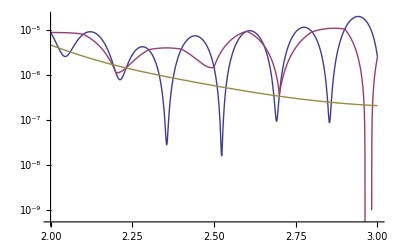

```mathematica
LogPlot[{temp[θ],interp3[θ],eik0interp3[θ]},{θ,2,3}]
```

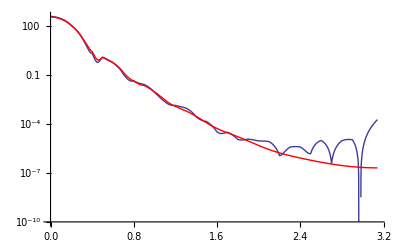

```mathematica
p3=LogPlot[interp3[θ],{θ,0,Pi}];
eik0p3=LogPlot[eik0interp3[θ],{θ,0,Pi},PlotStyle->Red];
Show[p3,eik0p3]
```

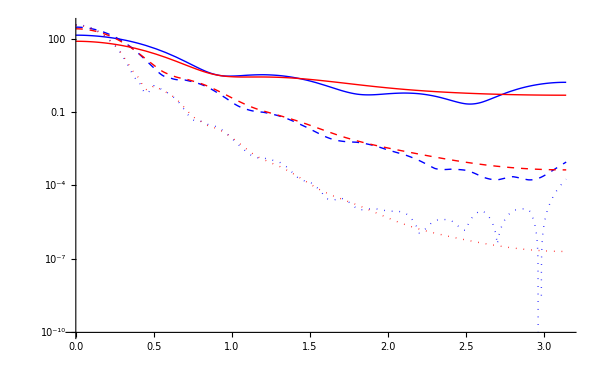

```mathematica
LogPlot[{interp1[θ],eik0interp1[θ],interp2[θ],eik0interp2[θ],interp3[θ],eik0interp3[θ]},{θ,0,Pi},PlotStyle->{{Blue},{Red},{Blue,Dashed},{Red,Dashed},{Blue,Dotted},{Red,Dotted}},PlotLegend->{"Partial Wave: k=1","Eikonal: k=1","Partial Wave: k=2","Eikonal: k=2","Partial Wave: k=3","Eikonal: k=3"},LegendPosition->{1.1,-0.4},LegendSize->{1,1},ImageSize->600]
```

The eikonal approximation actually appears to track the partial wave expansion quite well for k = 1, 2, and 3, but is again missing a lot of the finer structure.

## Plot for k=0.1

As you can see below, the approximation gets pretty bad as k -> 0.

```mathematica
Abs[f[.1,0]]^2
```

9.73572

```mathematica
Abs[Eif0[.1,0]]^2
```

2.19448

```mathematica
interp01=Interpolation[dσdΩ[.1]];
eik0interp01=Interpolation[eik0dσdΩ[.1]];
```

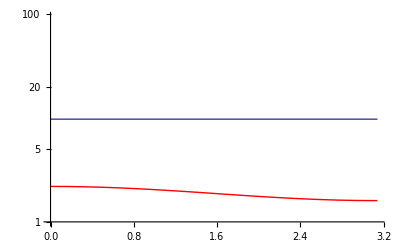

```mathematica
p01=LogPlot[interp01[θ],{θ,0,Pi}];
eik0p01=LogPlot[eik0interp01[θ],{θ,0,Pi},PlotStyle->Red];
Show[p01,eik0p01]
```

## Add in Eikonal Corrections

### First order correction

```mathematica
En[k_]:=(k*ℏc)^2/(2*m)
U[r_]:=V[r]/V0
ϵ[k_]:=V0/(2*En[k])
```

```mathematica
τ1[k_,b_]=-k*ϵ[k]^2*NIntegrate[Evaluate[(1#+b*D[#,b])&[U[Sqrt[z^2+b^2]]^2]],{z,0,15}];
```

```mathematica
T1[k_,b_]:=Exp[I(χ0[k,b]+τ1[k,b])]-1
Eif1[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T1[k,b],{b,0,15}]
```

```mathematica
eik1dσdΩ[k_]:=Table[{θ/10.,Abs[Eif1[k,θ/10]]^2},{θ,0,10*Pi,1}]
```

```mathematica
eik1dσdΩ[1]
```

{{0,95.4916},{0.1,91.322},{0.2,79.8603},{0.3,63.8325},{0.4,46.6181},{0.5,31.1322},{0.6,19.1034},{0.7,10.9457},{0.8,6.10314},{0.9,3.58056},{1.,2.39601},{1.1,1.82978},{1.2,1.47535},{1.3,1.1702},{1.4,0.890037},{1.5,0.660611},{1.6,0.506438},{1.7,0.432378},{1.8,0.425104},{1.9,0.462055},{2.,0.520177},{2.1,0.581276},{2.2,0.633878},{2.3,0.672689},{2.4,0.696956},{2.5,0.708656},{2.6,0.711005},{2.7,0.707442},{2.8,0.701046},{2.9,0.694284},{3.,0.688937},{3.1,0.686134}}

```mathematica
eik1interp1=Interpolation[%];
```

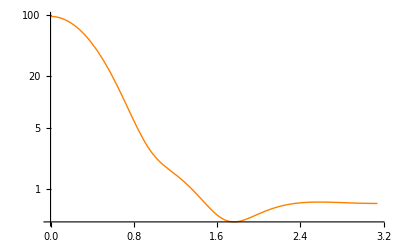

```mathematica
eik1p1=LogPlot[eik1interp1[θ],{θ,0,Pi},PlotStyle->Orange]
```

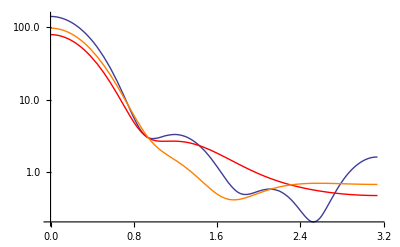

```mathematica
Show[p1,eik0p1,eik1p1]
```

### Second order correction

```mathematica
τ2[k_,b_]=-k*ϵ[k]^3*NIntegrate[Evaluate[(1#+5/3*b*D[#,b]+1/3*b^2*D[#,{b,2}])&[U[Sqrt[z^2+b^2]]^3]],{z,0,15}]-b*D[χ0[k,b],b]^3/(24*k^2);
ω2[k_,b_]=D[χ0[k,b],b]*D[b*D[χ0[k,b],b],b]/(8*k^2);
```

```mathematica
T2[k_,b_]:=Exp[I(χ0[k,b]+τ1[k,b]+τ2[k,b])]*Exp[-ω2[k,b]]-1
Eif2[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T2[k,b],{b,0,15}]
```

```mathematica
eik2dσdΩ[k_]:=Table[{θ/10.,Abs[Eif2[k,θ/10]]^2},{θ,0,10*Pi,1}]
```

```mathematica
eik2dσdΩ[1]
```

{{0,112.031},{0.1,106.896},{0.2,92.7954},{0.3,73.1305},{0.4,52.1158},{0.5,33.3836},{0.6,19.0774},{0.7,9.68851},{0.8,4.48572},{0.9,2.17948},{1.,1.49308},{1.1,1.47992},{1.2,1.59394},{1.3,1.60884},{1.4,1.48934},{1.5,1.28093},{1.6,1.04232},{1.7,0.816281},{1.8,0.624604},{1.9,0.473341},{2.,0.359865},{2.1,0.278148},{2.2,0.221665},{2.3,0.184574},{2.4,0.161982},{2.5,0.149865},{2.6,0.14493},{2.7,0.144507},{2.8,0.146481},{2.9,0.149244},{3.,0.151644},{3.1,0.152952}}

```mathematica
eik2interp1=Interpolation[%];
```

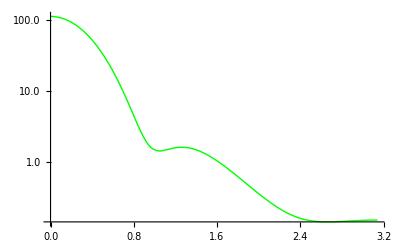

```mathematica
eik2p1=LogPlot[eik2interp1[θ],{θ,0,Pi},PlotStyle->Green]
```

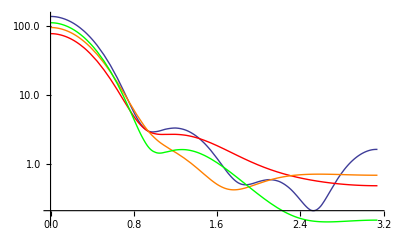

```mathematica
Show[p1,eik0p1,eik1p1,eik2p1,PlotRange->Automatic]
```

### Third order correction

```mathematica
τ3[k_,b_]=-k*ϵ[k]^4*NIntegrate[Evaluate[(5/4#+11/4*b*D[#,b]+b^2*D[#,{b,2}]+1/12*b^3*D[#,{b,3}])&[U[Sqrt[z^2+b^2]]^4]],{z,0,15}]-b*D[τ1[k,b],b]*D[χ0[k,b],b]^2/(8*k^2);
ϕ3[k_,b_]=-k*ϵ[k]^2*NIntegrate[Evaluate[(1#+5/3*b*D[#,b]+1/3*b^2*D[#,{b,2}])&[(1/(2*k)*D[U[Sqrt[z^2+b^2]],b])^2]],{z,0,15}];
ω3[k_,b_]=(D[χ0[k,b],b]*D[b*D[τ1[k,b],b],b]+D[τ1[k,b],b]*D[b*D[χ0[k,b],b],b])/(8*k^2);
```

```mathematica
T3[k_,b_]:=Exp[I*(χ0[k,b]+τ1[k,b]+τ2[k,b]+τ3[k,b]+ϕ3[k,b])]*Exp[-(ω2[k,b]+ω3[k,b])]-1
```

```mathematica
Eif3[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T3[k,b],{b,0,15}]
```

```mathematica
eik3dσdΩ[k_]:=Table[{θ/10.,Abs[Eif3[k,θ/10]]^2},{θ,0,10*Pi,1}]
```

```mathematica
eik3dσdΩ[1]
```

{{0,91.4445},{0.1,86.934},{0.2,74.6354},{0.3,57.7358},{0.4,40.1192},{0.5,25.0115},{0.6,14.1374},{0.7,7.6284},{0.8,4.51711},{0.9,3.43732},{1.,3.19103},{1.1,3.02504},{1.2,2.63931},{1.3,2.04368},{1.4,1.3837},{1.5,0.810046},{1.6,0.414108},{1.7,0.217378},{1.8,0.190413},{1.9,0.279713},{2.,0.429794},{2.1,0.596037},{2.2,0.749131},{2.3,0.87404},{2.4,0.966433},{2.5,1.02867},{2.6,1.06643},{2.7,1.08638},{2.8,1.09476},{2.9,1.09671},{3.,1.09604},{3.1,1.09518}}

```mathematica
eik3interp1=Interpolation[%];
```

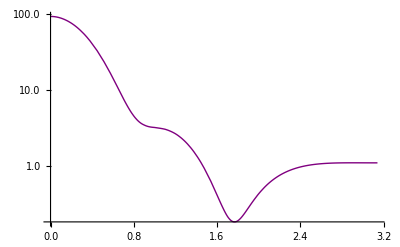

```mathematica
eik3p1=LogPlot[eik3interp1[θ],{θ,0,Pi},PlotStyle->Purple]
```

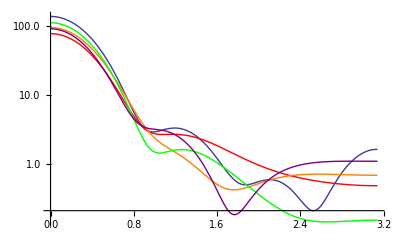

```mathematica
Show[p1,eik0p1,eik1p1,eik2p1,eik3p1,PlotRange->Automatic]
```

### Eikonal to third order for k = 1, 2, 3

```mathematica
eik1dσdΩ[2]
```

NIntegrate::inumr: The integrand -39.42463943157022`  + 7.884927886314045` ⅈ/1 + ⅇ^1.8518518518518516` (-3 + √Plus[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand 1.`  + 0.` ⅈ/(1 + ⅇ^1.8518518518518516` (-3 + « 1 »))^2 - (3.7037037037037033`  + 0.` ⅈ) b^2 ⅇ^1.8518518518518516` (-3 + √Power[« 1 »] + « 1 »)/(1 + ⅇ^1.8518518518518516` « 1 »)^3 √b^2 + z^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{{0,293.229},{0.1,253.737},{0.2,163.545},{0.3,77.1219},{0.4,25.8275},{0.5,6.47019},{0.6,2.40483},{0.7,1.97084},{0.8,1.44185},{0.9,0.772509},{1.,0.346935},{1.1,0.179203},{1.2,0.127405},{1.3,0.0983604},{1.4,0.0691364},{1.5,0.0442011},{1.6,0.0277238},{1.7,0.01859},{1.8,0.0137187},{1.9,0.010736},{2.,0.00851045},{2.1,0.00669704},{2.2,0.00524199},{2.3,0.00413013},{2.4,0.00331794},{2.5,0.00274219},{2.6,0.00234029},{2.7,0.00206183},{2.8,0.00187093},{2.9,0.00174416},{3.,0.00166718},{3.1,0.001632}}

```mathematica
eik1interp2=Interpolation[%];
```

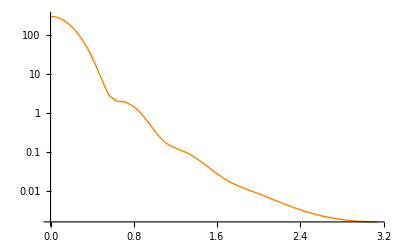

```mathematica
eik1p2=LogPlot[eik1interp2[θ],{θ,0,Pi},PlotStyle->Orange]
```

```mathematica
eik2dσdΩ[2]
```

NIntegrate::inumr: The integrand -39.42463943157022`  + 7.884927886314045` ⅈ/1 + ⅇ^1.8518518518518516` (-3 + √Plus[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand 1.`  + 0.` ⅈ/(1 + ⅇ^1.8518518518518516` (-3 + « 1 »))^2 - (3.7037037037037033`  + 0.` ⅈ) b^2 ⅇ^1.8518518518518516` (-3 + √Power[« 1 »] + « 1 »)/(1 + ⅇ^1.8518518518518516` « 1 »)^3 √b^2 + z^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{{0,294.891},{0.1,254.649},{0.2,163.044},{0.3,75.9351},{0.4,24.9955},{0.5,6.30489},{0.6,2.57006},{0.7,2.09458},{0.8,1.42198},{0.9,0.684686},{1.,0.273226},{1.1,0.143963},{1.2,0.117926},{1.3,0.0974434},{1.4,0.0684081},{1.5,0.0426767},{1.6,0.0269085},{1.7,0.0195534},{1.8,0.0164681},{1.9,0.0146459},{2.,0.0128563},{2.1,0.0109482},{2.2,0.00912235},{2.3,0.00756008},{2.4,0.00632944},{2.5,0.00541192},{2.6,0.00475075},{2.7,0.00428453},{2.8,0.00396253},{2.9,0.00374836},{3.,0.00361844},{3.1,0.00355914}}

```mathematica
eik2interp2=Interpolation[%];
```

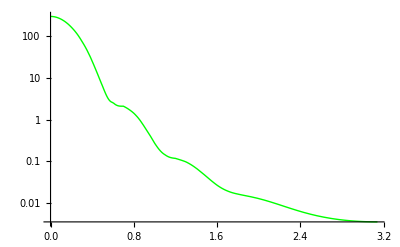

```mathematica
eik2p2=LogPlot[eik2interp2[θ],{θ,0,Pi},PlotStyle->Green]
```

```mathematica
eik3dσdΩ[2]
```

NIntegrate::inumr: The integrand -39.42463943157022`  + 7.884927886314045` ⅈ/1 + ⅇ^1.8518518518518516` (-3 + √Plus[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand 1.`  + 0.` ⅈ/(1 + ⅇ^1.8518518518518516` (-3 + « 1 »))^2 - (3.7037037037037033`  + 0.` ⅈ) b^2 ⅇ^1.8518518518518516` (-3 + √Power[« 1 »] + « 1 »)/(1 + ⅇ^1.8518518518518516` « 1 »)^3 √b^2 + z^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{{0,294.867},{0.1,254.726},{0.2,163.303},{0.3,76.2613},{0.4,25.2329},{0.5,6.39604},{0.6,2.55184},{0.7,2.03178},{0.8,1.36394},{0.9,0.65195},{1.,0.261367},{1.1,0.138152},{1.2,0.107907},{1.3,0.08268},{1.4,0.0537613},{1.5,0.0322565},{1.6,0.0215244},{1.7,0.0176819},{1.8,0.0161767},{1.9,0.0147172},{2.,0.0129065},{2.1,0.0110678},{2.2,0.00951451},{2.3,0.00835394},{2.4,0.00754412},{2.5,0.00699088},{2.6,0.00660726},{2.7,0.00633332},{2.8,0.0061345},{2.9,0.00599355},{3.,0.005903},{3.1,0.00586009}}

```mathematica
eik3interp2=Interpolation[%];
```

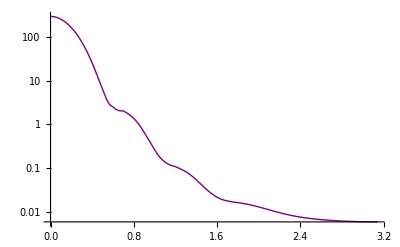

```mathematica
eik3p2=LogPlot[eik3interp2[θ],{θ,0,Pi},PlotStyle->Purple]
```

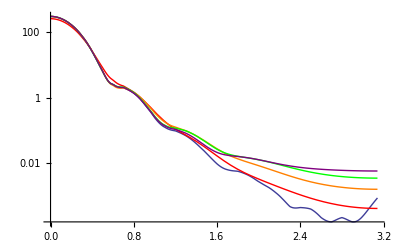

```mathematica
Show[p2,eik0p2,eik1p2,eik2p2,eik3p2]
```

```mathematica
eik1dσdΩ[3]
```

NIntegrate::inumr: The integrand -39.42463943157022`  + 7.884927886314045` ⅈ/1 + ⅇ^1.8518518518518516` (-3 + √Plus[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand 1.`  + 0.` ⅈ/(1 + ⅇ^1.8518518518518516` (-3 + « 1 »))^2 - (3.7037037037037033`  + 0.` ⅈ) b^2 ⅇ^1.8518518518518516` (-3 + √Power[« 1 »] + « 1 »)/(1 + ⅇ^1.8518518518518516` « 1 »)^3 √b^2 + z^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{{0,374.138},{0.1,274.827},{0.2,105.998},{0.3,19.2216},{0.4,1.99512},{0.5,1.22341},{0.6,0.57887},{0.7,0.123655},{0.8,0.0445765},{0.9,0.0301565},{1.,0.0119942},{1.1,0.00370552},{1.2,0.00199877},{1.3,0.00125574},{1.4,0.000587395},{1.5,0.000244121},{1.6,0.000131493},{1.7,0.0000869334},{1.8,0.000053933},{1.9,0.000030146},{2.,0.0000167752},{2.1,0.0000103918},{2.2,7.26747×10^-6},{2.3,5.39165×10^-6},{2.4,4.05011×10^-6},{2.5,3.05423×10^-6},{2.6,2.3388×10^-6},{2.7,1.84691×10^-6},{2.8,1.52175×10^-6},{2.9,1.31618×10^-6},{3.,1.19699×10^-6},{3.1,1.1442×10^-6}}

```mathematica
eik1interp3=Interpolation[%];
```

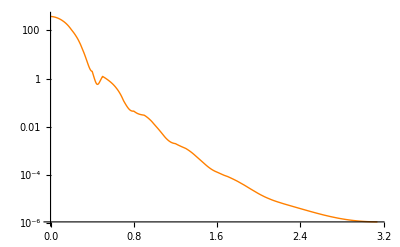

```mathematica
eik1p3=LogPlot[eik1interp3[θ],{θ,0,Pi},PlotStyle->Orange]
```

```mathematica
eik2dσdΩ[3]
```

NIntegrate::inumr: The integrand -39.42463943157022`  + 7.884927886314045` ⅈ/1 + ⅇ^1.8518518518518516` (-3 + √Plus[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand 1.`  + 0.` ⅈ/(1 + ⅇ^1.8518518518518516` (-3 + « 1 »))^2 - (3.7037037037037033`  + 0.` ⅈ) b^2 ⅇ^1.8518518518518516` (-3 + √Power[« 1 »] + « 1 »)/(1 + ⅇ^1.8518518518518516` « 1 »)^3 √b^2 + z^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{{0,373.822},{0.1,274.315},{0.2,105.467},{0.3,19.0624},{0.4,2.02441},{0.5,1.2095},{0.6,0.543894},{0.7,0.111024},{0.8,0.0428305},{0.9,0.0281936},{1.,0.0103956},{1.1,0.00335534},{1.2,0.00213821},{1.3,0.00135794},{1.4,0.00062945},{1.5,0.000292072},{1.6,0.000190363},{1.7,0.000137848},{1.8,0.0000888745},{1.9,0.0000524075},{2.,0.0000320027},{2.1,0.0000221226},{2.2,0.0000168856},{2.3,0.0000132998},{2.4,0.0000104517},{2.5,8.19866×10^-6},{2.6,6.51226×10^-6},{2.7,5.31722×10^-6},{2.8,4.5083×10^-6},{2.9,3.98736×10^-6},{3.,3.68128×10^-6},{3.1,3.54466×10^-6}}

```mathematica
eik2interp3=Interpolation[%];
```

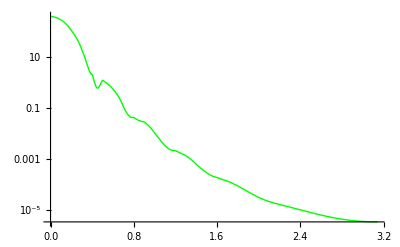

```mathematica
eik2p3=LogPlot[eik2interp3[θ],{θ,0,Pi},PlotStyle->Green]
```

```mathematica
eik3dσdΩ[3]
```

NIntegrate::inumr: The integrand -39.42463943157022`  + 7.884927886314045` ⅈ/1 + ⅇ^1.8518518518518516` (-3 + √Plus[« 2 »]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand 1.`  + 0.` ⅈ/(1 + ⅇ^1.8518518518518516` (-3 + « 1 »))^2 - (3.7037037037037033`  + 0.` ⅈ) b^2 ⅇ^1.8518518518518516` (-3 + √Power[« 1 »] + « 1 »)/(1 + ⅇ^1.8518518518518516` « 1 »)^3 √b^2 + z^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{{0,373.882},{0.1,274.408},{0.2,105.556},{0.3,19.0824},{0.4,2.01275},{0.5,1.2013},{0.6,0.539485},{0.7,0.108083},{0.8,0.0404853},{0.9,0.026123},{1.,0.00913545},{1.1,0.00281383},{1.2,0.00181942},{1.3,0.00110967},{1.4,0.000497961},{1.5,0.000256272},{1.6,0.000188055},{1.7,0.000138832},{1.8,0.0000918617},{1.9,0.0000600539},{2.,0.0000428103},{2.1,0.0000332308},{2.2,0.0000266661},{2.3,0.0000214836},{2.4,0.0000173677},{2.5,0.0000142355},{2.6,0.0000119462},{2.7,0.0000103198},{2.8,9.19329×10^-6},{2.9,8.44371×10^-6},{3.,7.98935×10^-6},{3.1,7.78217×10^-6}}

```mathematica
eik3interp3=Interpolation[%];
```

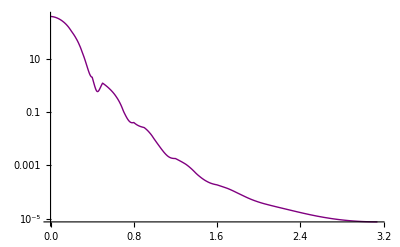

```mathematica
eik3p3=LogPlot[eik3interp3[θ],{θ,0,Pi},PlotStyle->Purple]
```

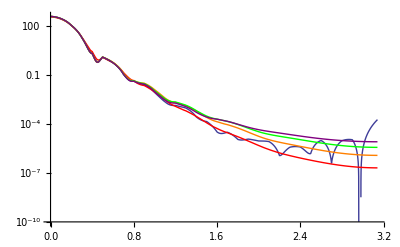

```mathematica
Show[p3,eik0p3,eik1p3,eik2p3,eik3p3]
```